```mathematica
Exponencialni:
```

```mathematica
ClearAll[α,σ,μ,x];
```

```mathematica
p = 1/σ*Exp[-(x-μ)/(σ)]
```

ⅇ^((-x+μ)/σ)/σ

```mathematica
θ = σ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

-(-x+μ+σ)/σ^2

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

(-2 x+2 μ+σ)/σ^3

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

-((ⅇ^((-x+μ)/σ)/σ)^(1+α) (-x+μ+σ))/σ^2

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(-x+μ)-> -y*σ]
```

ⅇ^y (-1+y) (ⅇ^-y/σ)^(2+α)

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,0,∞}]]
```

ConditionalExpression[-(α (1/σ)^(1+α))/(1+α)^2,Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

(ⅇ^((-x+μ)/σ)/σ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(-x+μ)-> -y*σ]
```

(ⅇ^-y/σ)^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,0,∞}]]
```

ConditionalExpression[(1/σ)^α/(1+α),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[-α/(σ+α σ),Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[α/((1+α) σ^2),Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[((ⅇ^((-x+μ)/σ)/σ)^(1+α) (α (x-μ)^2-(2 (1+2 α) (x-μ) σ)/(1+α)+((1+2 α) σ^2)/(1+α)^2))/σ^4,Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(-x+μ)->-y*σ]
```

ConditionalExpression[((ⅇ^-y/σ)^(1+α) (α (x-μ)^2-(2 (1+2 α) (x-μ) σ)/(1+α)+((1+2 α) σ^2)/(1+α)^2))/σ^4,Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Ia1/.(x-μ)->y*σ]
```

ConditionalExpression[((1+2 α+y (1+α) (-2+α (-4+y+y α))) (ⅇ^-y/σ)^(1+α))/((1+α)^2 σ^2),Re[α]>-1]

```mathematica
Ia3 = FullSimplify[Integrate[Ia2*σ,{y,0,∞}]]
```

ConditionalExpression[-(1/σ)^(2+α)/(1+α)^3,Re[α]>-1]

```mathematica
IF = FullSimplify[-Ia3^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(1+α)^2 ((1+α) (x-μ)-σ) (1/σ)^-α (ⅇ^((-x+μ)/σ)/σ)^α,Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.μ->0]
```

ConditionalExpression[(1+α)^2 (x+x α-σ) (1/σ)^-α (ⅇ^(-x/σ)/σ)^α,Re[α]>-1]

```mathematica
IFun = Function[{σ,α} ,(1+α)^2 (x+x α-σ) (1/σ)^-α (ⅇ^(-x/σ)/σ)^α];
```

```mathematica
Needs["PlotLegends`"]
```

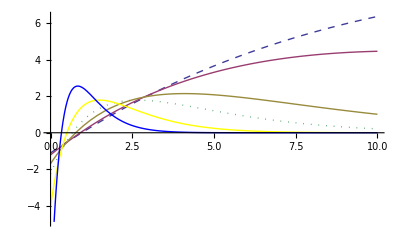

```mathematica
Plot[{
IFun[1,0.05],
IFun[1,0.1],
IFun[1,0.3],
IFun[1,0.5],
IFun[1,1],
IFun[1,2]},
{x,0,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```

```mathematica
Exponencialni:
```

```mathematica
ClearAll[α,σ,μ,x];
```

```mathematica
θ = μ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

1/σ

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

0

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

((ⅇ^((-x+μ)/σ)/σ)^(1+α))/σ

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(-x+μ)-> -y*σ]
```

ⅇ^y (ⅇ^-y/σ)^(2+α)

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,0,∞}]]
```

ConditionalExpression[(1/σ)^(1+α)/(1+α),Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

(ⅇ^((-x+μ)/σ)/σ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(-x+μ)->-y*σ]
```

(ⅇ^-y/σ)^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,0,∞}]]
```

ConditionalExpression[(1/σ)^α/(1+α),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[1/σ,Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ,{y,0,∞}]]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ (ⅇ^-x + μ/σ/σ)^α\ ComplexInfinity encountered.

ConditionalExpression[Indeterminate,Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.σ->1]
```

ConditionalExpression[(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ),Re[α]>-1]

```mathematica
IFun = Function[{μ,α} ,(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ)];
```

```mathematica
Needs["PlotLegends`"]
```

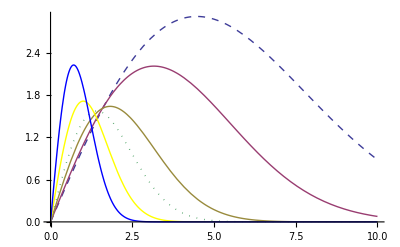

```mathematica
Plot[{
IFun[0,0.05],
IFun[0,0.1],
IFun[0,0.3],
IFun[0,0.5],
IFun[0,1],
IFun[0,2]},
{x,0,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```